```mathematica
link=Install[LinkConnect["42045@192.168.150.128,35995@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωe=-1836,θr=0.45,θe=Sqrt[0.9],θb=0.045,ωb=15*Sqrt[0.9],ωe=15*Sqrt[1836],
ωp ={0.039893,0.143882,0.348679,0.597894,0.815419,0.984766,1.11653,1.21888,1.29599,1.34998,1.38201,1.39263,1.38201,1.34998,1.29599,1.21888,1.11653,0.984766,0.815419,0.597894,0.348679,0.143882,0.039893},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd,vr]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe},{ωb,ωe},{θb,θe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
sol=With[{k=13.15,wna=85Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[14,0.015] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

```mathematica
sol=With[{k=Range[12.6,13.2,0.05],wna=85Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[13.2,-0.02] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

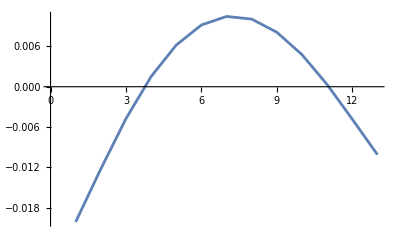

```mathematica
ListLinePlot[Im[sol[[2,2]]]]
```

```mathematica
gama={};
with[{k=Range[13]},gama=Append[gama,Im[sol[[2,2,k]]]]];
Export["15.txt",gama];
```

```mathematica
check=With[{k=Range[12.9,12.6,-0.05],wna=85Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[13.5,0.011] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

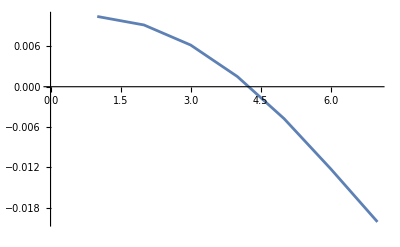

```mathematica
ListLinePlot[Im[check[[2,2]]]]
```